## In this notebook, I find the mean and standard deviation for the diagonal and off-diagonal elements of B, C, and Sigma. I also have the generating functions based on that data listed here, which are also found in functions.nb

```mathematica
NotebookEvaluate["/Users/claireplunkett/Documents/REU/MAR_dataruns0.nb"];
```

MAR_functions evaluation complete!

Inverse::luc: Result for Inverse of badly conditioned matrix {{25.,125.266,-37.589,98.6679,28.6072},{125.266,627.662,-188.345,494.389,143.34},{-37.589,-188.345,194.168,-160.508,-48.7982},{98.6679,494.389,-160.508,401.695,121.615},{28.6072,143.34,-48.7982,121.615,146.037}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

Inverse::luc: Result for Inverse of badly conditioned matrix {{25.,125.266,79.9162,79.7768,67.4355,107.138,21.1817,-65.0677},{125.266,627.662,400.431,399.733,337.895,536.831,106.134,-326.031},«5»,{-65.0677,-326.031,-258.173,-208.062,-211.884,-320.381,-27.886,263.632}} may contain significant numerical errors.

General::stop: Further output of Inverse::luc will be suppressed during this calculation.

## Getting Statistics

### Functions

```mathematica
offdiagonals[btype_,numbersquare_,range_]:=Module[{list},
If[numbersquare== 1,list=Flatten[DeleteCases[Flatten[UpperTriangularize[btype[#],1]+LowerTriangularize[btype[#],-1]],0.]&/@range],
list=Flatten[DeleteCases[Flatten[UpperTriangularize[btype[[#]],1]+LowerTriangularize[btype[[#]],-1]],0.]&/@range]
];
Print["Mean = ",Mean[list]];
Print["Standard Deviation = ",StandardDeviation[list]];
Show[SmoothHistogram[list,PlotRange->All]]
]
```

```mathematica
diagonals[btype_,numbersquare_,range_]:=Module[{list},
If[numbersquare== 1,list=Flatten[Diagonal[btype[#]]&/@range],
list=Flatten[Diagonal[btype[[#]]]&/@range]
];
Print["Mean = ",Mean[list]];
Print["Standard Deviation = ",StandardDeviation[list]];
Show[SmoothHistogram[list,PlotRange->All]]
]
```

```mathematica
allelements[btype_,numbersquare_,range_]:=Module[{list},
If[numbersquare== 1,list=Flatten[btype[#]&/@range],
list=Flatten[btype[[#]]&/@range]
];
Print["Mean = ",Mean[list]];
Print["Standard Deviation = ",StandardDeviation[list]];
Show[SmoothHistogram[list,PlotRange->All]]
]
```

### Composite

Mean = -0.0365901

Standard Deviation = 0.179791

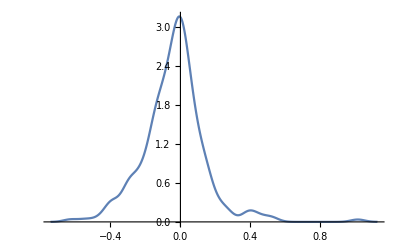

```mathematica
offdiagonals[bb,1,Range[16]]
```

Mean = -0.0384298

Standard Deviation = 0.178785

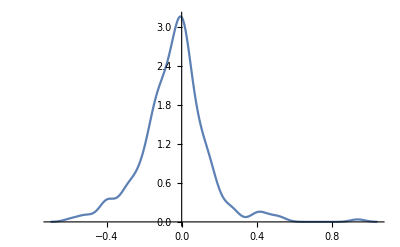

```mathematica
offdiagonals[bb,1,Range[18,33]]
```

Mean = 0.59429

Standard Deviation = 0.188138

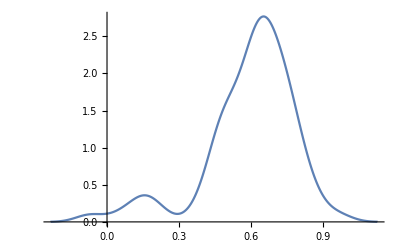

```mathematica
diagonals[bb,1,Range[16]]
```

Mean = 0.592574

Standard Deviation = 0.185722

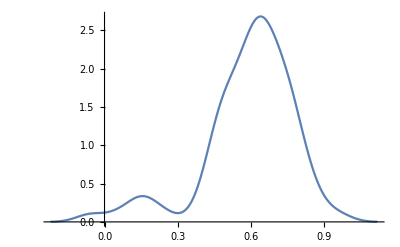

```mathematica
diagonals[bb,1,Range[18,33]]
```

### Individuals

Mean = -0.0356709

Standard Deviation = 0.475423

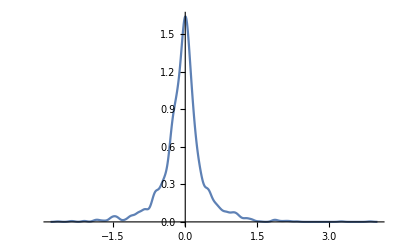

```mathematica
offdiagonals[bbA,2,Range[103]]
```

Mean = -0.0357539

Standard Deviation = 0.476132

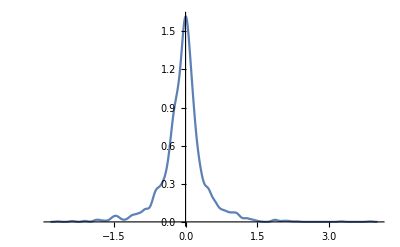

```mathematica
offdiagonals[bbAC,2,Range[103]]
```

Mean = 0.366474

Standard Deviation = 0.407773

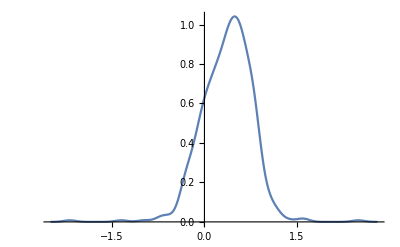

```mathematica
diagonals[bbA,2,Range[103]]
```

Mean = 0.369383

Standard Deviation = 0.408503

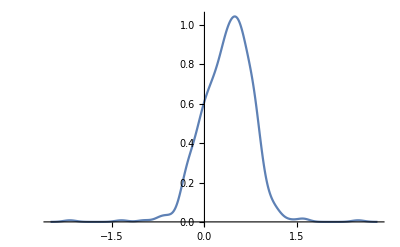

```mathematica
diagonals[bbAC,2,Range[103]]
```

### Averaged

Mean = -0.0362342

Standard Deviation = 0.237472

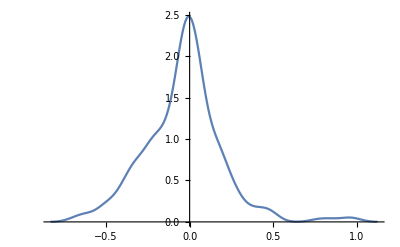

```mathematica
offdiagonals[bbavg,1,Range[16]]
```

```mathematica
offdiagonals[bbavg,1,Range[18,33]]
```

Mean = -0.0362342

Standard Deviation = 0.237472

-Graphics-

Mean = 0.398932

Standard Deviation = 0.216456

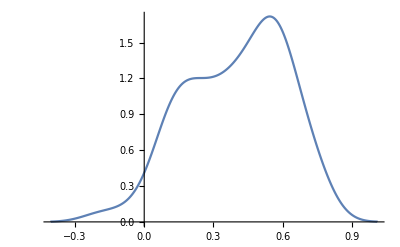

```mathematica
diagonals[bbavg,1,Range[16]]
```

```mathematica
diagonals[bbavg,1,Range[18,33]]
```

Mean = 0.398932

Standard Deviation = 0.216456

-Graphics-

### C

Mean = 0.0518599

Standard Deviation = 1.00001

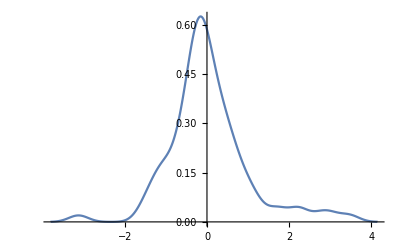

```mathematica
allelements[c,1,Range[18,33]]
```

## What About Sigma?

### Getting Statistics

```mathematica
findSigma[dataset0_,tank0_]:=Module[{size},
size=Dimensions[bb[dataset0]][[1]];
Partition[(IdentityMatrix[size^2]-KroneckerProduct[bb[dataset0],bb[dataset0]]).Flatten[Covariance[prodata[dataset0][[tank0]]]],size]
]
myCovariance[dataset0_]:=Module[{numberoftanks},
numberoftanks=Dimensions[prodata[dataset0]][[1]];
(Dimensions[prodata[dataset0]][[2]]-1)Sum[findSigma[dataset0,i],{i,1,numberoftanks}]/(numberoftanks Dimensions[prodata[dataset0]][[2]] - 1)
]
```

Mean = 0.459684

Standard Deviation = 0.972132

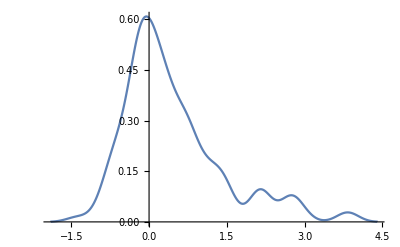

```mathematica
offdiagonals[myCovariance,1,Range[1,16]]
```

Mean = 2.89209

Standard Deviation = 1.88999

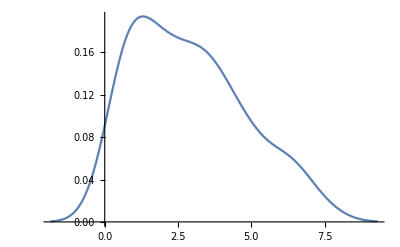

```mathematica
diagonals[myCovariance,1,Range[1,16]]
```

### From R Data

```mathematica
SetDirectory["/Users/claireplunkett/Documents/REU/MAR Results"];
For[i=1,i≤33,i++,
SigRraw[i]=Import[ToString[i]<>"/bestfit.process.errors.covariance.csv"]; (* R code does not give covariance of covariates *)
SigR[i]=Partition[SigRraw[i][[2;;-1,3]],Sqrt[Dimensions[SigRraw[i]][[1]]-1]];
]
```

```mathematica
SigR[20]
```

{{4.08639,1.44257,-0.0302974,-0.0618725},{1.44257,3.60713,-0.131115,-0.597491},{-0.0302974,-0.131115,0.938114,0.954804},{-0.0618725,-0.597491,0.954804,4.16135}}

Mean = 0.479896

Standard Deviation = 0.98371

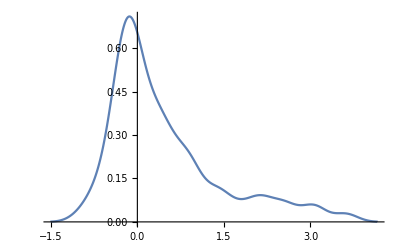

```mathematica
offdiagonals[SigR,1,Range[33]]
```

Mean = 3.22144

Standard Deviation = 1.97698

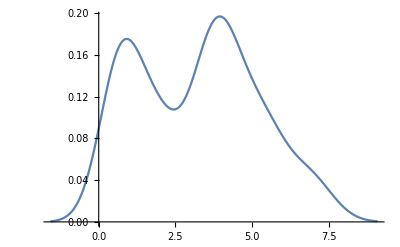

```mathematica
diagonals[SigR,1,Range[33]]
```

```mathematica
SigR[1]//MatrixForm
```

(5.65754 | 0.0716117 | 0.567451
0.0716117 | 0.944692 | 0.725913
0.567451 | 0.725913 | 3.62904)

```mathematica
SigR[2]//MatrixForm
```

(6.00163 | 0.491963 | -0.329697 | -0.203489
0.491963 | 3.35538 | -0.272501 | -0.741794
-0.329697 | -0.272501 | 0.808403 | 0.976999
-0.203489 | -0.741794 | 0.976999 | 5.70495)

```mathematica
Det[VinfR[3]]
```

960.61

```mathematica
Det[SigR[3]]
```

37.0759

### Function

```mathematica
GenPreSigma[p_]:=Module[{diags,preSig,Sig,b,i},
diags=DiagonalMatrix[RandomVariate[NormalDistribution[3.22144,1.97698],p]/2];
preSig=UpperTriangularize[RandomVariate[NormalDistribution[0.479896, 0.98371],{p,p}],1];
Sig=diags+preSig;
Sig=Sig+Transpose[Sig]
]
GenSigma[p_]:=Module[{Sig},
Sig=GenPreSigma[p];
While[Not[PositiveSemidefiniteMatrixQ[Sig]],Sig=GenPreSigma[p]];
Sig
]
```

## Generating Functions

```mathematica
GenPreBComposite[p_]:=Module[{diags,preB,B,b,i},
diags=RandomVariate[NormalDistribution[0.59257,0.18572],p];
preB=RandomVariate[NormalDistribution[-0.03843,0.17879],{p,p-1}];
B={};
For[i=1,i≤p,i++,
b=Insert[preB[[i]],diags[[i]],i];
B=Join[B,{b}]
];
B
]
GenBComposite[p_]:=Module[{B},
B=GenPreBComposite[p];
While[Max[Abs[Eigenvalues[B]]]≥1,B=GenPreBComposite[p]];
B
]
```

```mathematica
GenPreBIndividual[p_]:=Module[{diags,preB,B,b,i},
diags=RandomVariate[NormalDistribution[0.36938,0.40850],p];
preB=RandomVariate[NormalDistribution[-0.03575, 0.47613],{p,p-1}];
B={};
For[i=1,i≤p,i++,
b=Insert[preB[[i]],diags[[i]],i];
B=Join[B,{b}]
];
B
]
GenBIndividual[p_]:=Module[{B},
B=GenPreBIndividual[p];
While[Max[Abs[Eigenvalues[B]]]≥1,B=GenPreBIndividual[p]];
B
]
```

```mathematica
GenPreBAveraged[p_]:=Module[{diags,preB,B,b,i},
diags=RandomVariate[NormalDistribution[0.39893,0.21646],p];
preB=RandomVariate[NormalDistribution[-0.03623, 0.23747],{p,p-1}];
B={};
For[i=1,i≤p,i++,
b=Insert[preB[[i]],diags[[i]],i];
B=Join[B,{b}]
];
B
]
GenBAveraged[p_]:=Module[{B},
B=GenPreBAveraged[p];
While[Max[Abs[Eigenvalues[B]]]≥1,B=GenPreBAveraged[p]];
B
]
```

```mathematica
GenC[p_,d_]:=Module[{cmat},
cmat=RandomVariate[NormalDistribution[],{p,d}]
]
```